0.149776

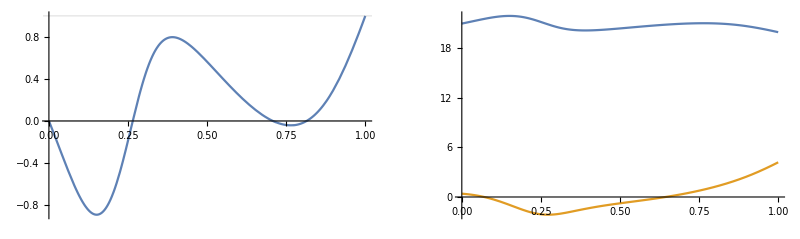

```mathematica
a=20+0.2I;b=1+0.2I;
ObstacleSize[a,b]
GraphicsRow[{
ObstaclePlot[a,b],
Plot[{Re[MulSum[a,b,n]],Im[MulSum[a,b,n]]},{n,0,1},PlotRange->Full]
}]
```

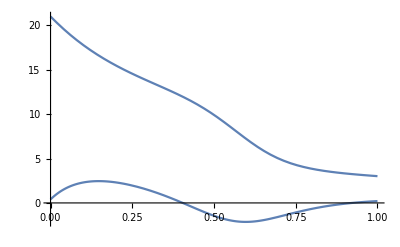

```mathematica
Plot[FracExp[a,-n]+FracExp[b,-n]//ReIm,{n,0,1}]
```

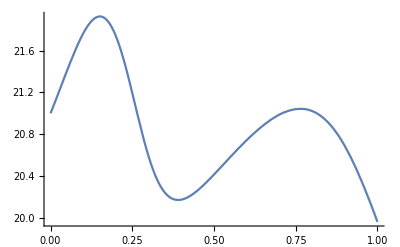

```mathematica
Plot[FracExp[FracExp[a,-n]+FracExp[b,-n],n]//Re,{n,0,1}]
```